## Kapitola 2 - Dopřední síť a umělá data Sin(x)

Demonstrace použití dopředné neuronové sítě na umělých datech - aproximace funkce sinus.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
Needs["NeuralNetworks`"]
```

## Vytvoření trénovacích dat

Vygenerujeme si umělá data - navzorkujeme sinusovku.

```mathematica
n=20;
x=Table[N[2π/(n-1) i],{i,0,n-1}];
y=Sin[x];
```

Takto vypadají naše data :

```mathematica
x
```

{0.,0.330694,0.661388,0.992082,1.32278,1.65347,1.98416,2.31486,2.64555,2.97625,3.30694,3.63763,3.96833,4.29902,4.62972,4.96041,5.2911,5.6218,5.95249,6.28319}

```mathematica
y
```

{0.,0.324699,0.614213,0.837166,0.9694,0.996584,0.915773,0.735724,0.475947,0.164595,-0.164595,-0.475947,-0.735724,-0.915773,-0.996584,-0.9694,-0.837166,-0.614213,-0.324699,-2.44929×10^-16}

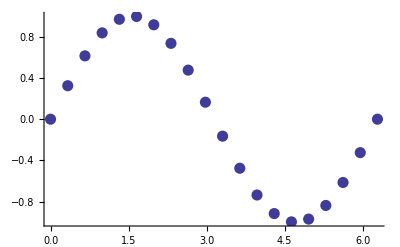

```mathematica
ListPlot[Transpose[{x,y}],PlotStyle->PointSize[0.02]]
```

## Zpracování dat neuronovou sítí

Inicializace sítě - zadáme trénovací množinu a počet neuronů. Počet neuronů se zadává jako seznam, každý prvek (číslo) seznamu odpovídá počtu neuronů v jedné skryté vrstvě. {3} znamená jedna skrytá vrstva s třemi neurony. {4,3} znamená dvě skryté vrstvy, jedna se čtyřmi neurony a druhá se třemi neurony.

Vytvořenou síť si uložíme do proměnné "net".

```mathematica
net=InitializeFeedForwardNet[x,y,{3},RandomInitialization->True]
```

FeedForwardNet[{{w1,w2}},{Neuron → Sigmoid, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2008, 6, 16, 13, 37, 38.5625}, OutputNonlinearity → None, NumberOfInputs → 1}]

Můžeme si nechat zobrazit nějaké další informace o vytvořené síti.

```mathematica
NetInformation[net]
```

FeedForward network created 2008-6-16 at 13:37. The network has 1 input and 1 output. It consists of 1 hidden layer with 3 neurons with activation function of Sigmoid type.

Podíváme se jak naše, zatím náhodně inicializovaná, síť odpovídá na data.

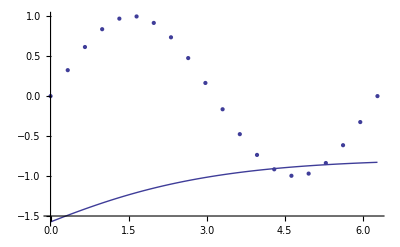

```mathematica
NetPlot[net,x,y]
```

Teď síť natrénujeme pomocí funkce "NeuralFit", které zadáme naší síť (proměnná "net"), trénovací množinu “x” a “y”, x jsou vstupní data, y jsou výstupní data a ještě zadáme počet učících kroků.

Funkce NeuralFit vyprodukuje naučenou síť a záznam o průběhu učení (může se hodit) - obě tyto návratové hodnoty si ukládáme (do proměnnée "net2" a "record").

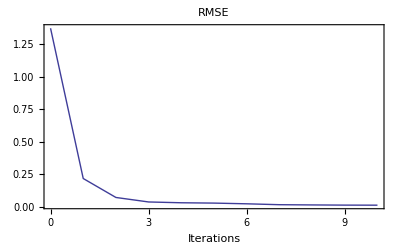

```mathematica
{net2,record}=NeuralFit[net,x,y,10];
```

Jak teď odpovídá natrénovaná síť (reprezentováno čarou) na data (body) :

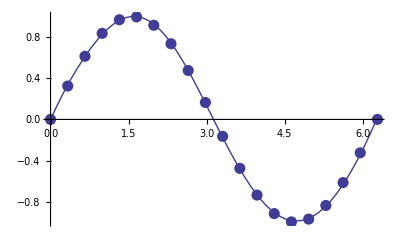

```mathematica
NetPlot[net2,x,y,PlotStyle->PointSize[0.02]]
```

Podíváme se i mimo trénovaný interval :

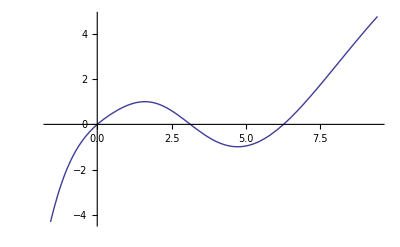

```mathematica
Plot[net2[{x}],{x,-π/2,3π}]
```

Můžeme se podívat na odpověď sítě na tzv. "data/model" diagramu - ideálně by měl být reprezentován čarou odpovídající ose 1. a 3. kvadrantu.

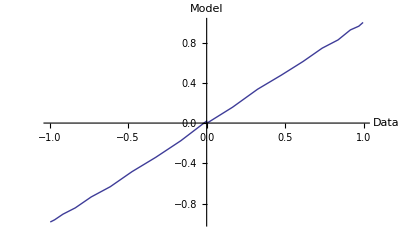

```mathematica
NetPlot[net2,x,y,DataFormat->NetOutput]
```

Takto potom vypadá síť, když ji převedeme do vzorce - určitě poznáváte aktivační funkce neuronu.

```mathematica
net2[{vstup}][[1]]
```

11.3665-534.635/(1+ⅇ^(0.782324+0.324938 vstup))+404.093/(1+ⅇ^(0.0789979+0.464389 vstup))-57.0133/(1+ⅇ^(-0.665781+0.827525 vstup))

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.